### Distributions: Estimate Multivariate Nonparametric Probabilities and Expectations

The PDF of a bivariate density estimate, using SmoothKernelDistribution, shown with the data it was created from and the expected values of successive power sums.

```mathematica
dist=MixtureDistribution[{2,.1},{MultinormalDistribution[-1 {1,1},2 IdentityMatrix[2]],MultinormalDistribution[2 {.5,.5},.01 IdentityMatrix[2]]}];
BlockRandom[SeedRandom[15];data=RandomVariate[dist,250]];
```

```mathematica
𝒟=SmoothKernelDistribution[data];
```

```mathematica
pdf=Show[Plot3D[Evaluate@PDF[𝒟,{x,y}],{x,-6,5},{y,-6,5},PlotRange->{{-6,5},{-6,5},All},ColorFunction->(Opacity[Rescale[#3,{0,.6},{0,1}],ColorData["DeepSeaColors"][#3]]&),Mesh->45,MeshStyle->Gray,MeshFunctions->{#3&},PlotPoints->50,ImageSize->550,ViewPoint->{Pi,-Pi,1}],ListPointPlot3D[Partition[Flatten[Transpose[{data,ConstantArray[0,Length[data]]}]],3],PlotStyle->Directive[PointSize->.0075]],AspectRatio->1,Boxed->False,Axes->None]
```

-Graphics3D-

### Curve Fitting: NonlinearModelFit

Simulate some data:

```mathematica
data=BlockRandom[SeedRandom[12345];Table[{x,Exp[-2.3 x/(11 +.4 x+x^2)]+RandomReal[{-.5,.5}]},{x,RandomReal[{1,15},20]}]];
```

Fit a nonlinear model to the data:

```mathematica
nlm=NonlinearModelFit[data,Exp[a x/(b+c x)],{a,b,c},x]
```

FittedModel[ⅇ^(-(2.16224 x)/(21.6536+4.50441 x))]

Obtain and visualize 90% confidence bands for the fit:

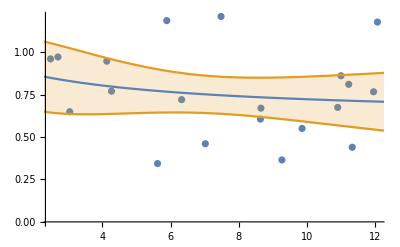

```mathematica
bands90[x_]=nlm["MeanPredictionBands",ConfidenceLevel->.9];
Show[ListPlot[data],Plot[{nlm[x],bands90[x]},{x,1,15},Filling->{2->{1}}]]
```

Obtain 95%, 99%, and 99.9% confidence bands:

```mathematica
{bands95[x_],bands99[x_],bands999[x_]}=Table[nlm["MeanPredictionBands",ConfidenceLevel->cl],{cl,{.95,.99,.999}}];
```

Visualize the confidence bands for the various levels:

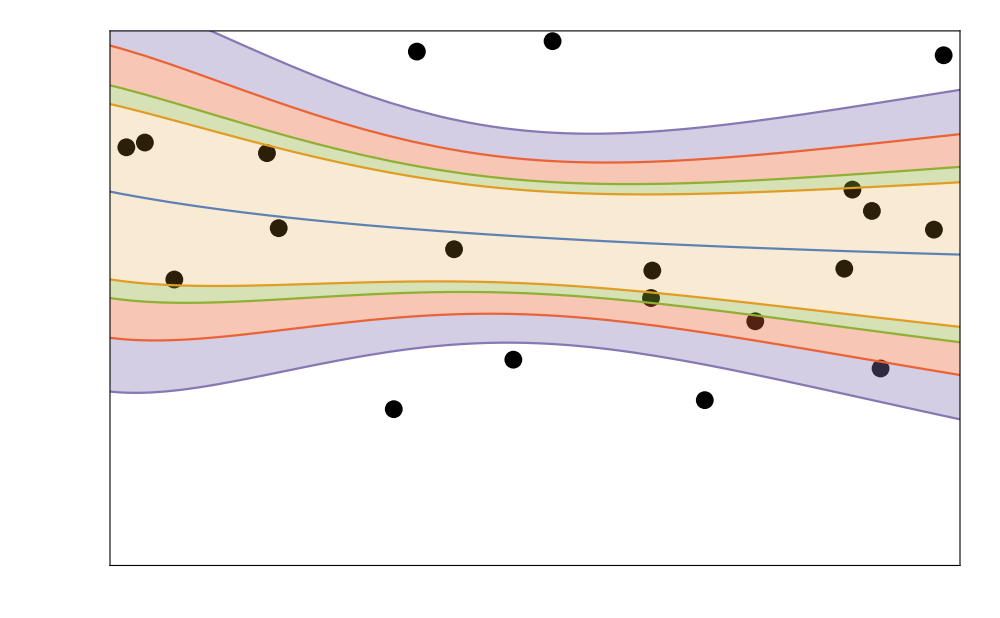

```mathematica
Show[ListPlot[data,PlotStyle->Black],Plot[{nlm[x],bands90[x],bands95[x],bands99[x],bands999[x]},{x,1,15},Filling->{2->{1},3->{2},4->{3},5->{4}}],ImageSize->1000,FrameTicks->None,Frame->True,FrameStyle->Directive[Black,Thick]]
```

### Advanced Curve Fitting: GeneralizedLinearModelFit

```mathematica
data=BlockRandom[SeedRandom[1];RandomReal[{.8,1},20]Table[(x-1)/(1+x),{x,20}]];
```

```mathematica
models=Map[Tooltip[Normal[GeneralizedLinearModelFit[data,{x,x^2},x,ExponentialFamily->"Binomial",LinkFunction->#]]]&,{"LogitLink","ProbitLink","LogLogLink","LogComplementLink","ComplementaryLogLogLink","OddsPowerLink"}];
```

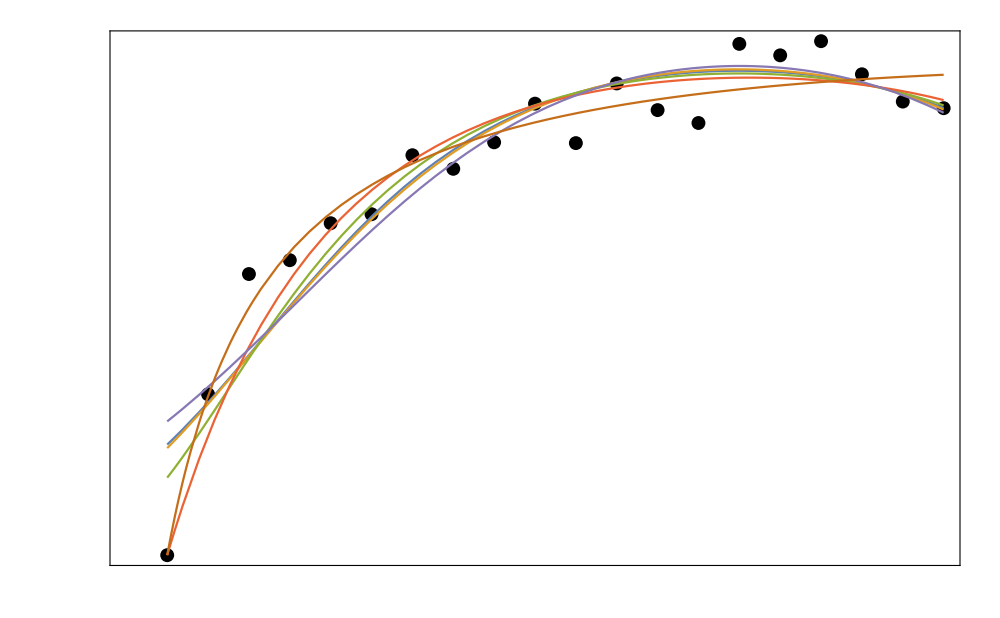

```mathematica
Show[ListPlot[data,PlotRange->All,PlotStyle->Directive[Black,PointSize[0.01]]],Plot[models,{x,1,20}],Frame->True,ImageSize->1000, FrameTicks->None,FrameStyle->Directive[Black,Thick]]
```